```mathematica
hepData=Import["/Users/samiyrjanheikki/Downloads/HEPData-ins617784-v1-csv/Table1.csv"];
pT=hepData[[All,1]];
σ=hepData[[All,4]];
pythia=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/pT_histogram.csv"];
pT2=pythia[[All,1]];
σ2=pythia[[All,2]];
```

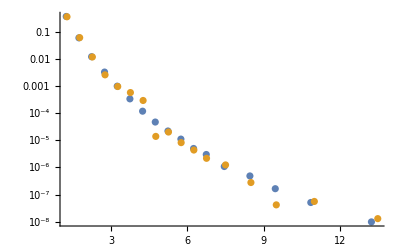

```mathematica
plot=Show[ListLogPlot[Transpose[{pT,σ}]],ListLogPlot[Transpose[{pT2,σ2}],PlotStyle->ColorData[97,"ColorList"][[2]]],PlotRange->All]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/sigma.pdf",plot]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/sigma.pdf